```mathematica
(* 检验 j0sh 的级数解. *)
j0sh[r_,z_,h_,H_]:=NIntegrate[BesselJ[0,r x]sh[x,h,H ,z ],{x,0,Infinity},Method->"ExtrapolatingOscillatory"];
j0shSeries[r_,z_,h_,H_,nmax_]:=Sum[2./H Sin[(n Pi h)/H]Sin[(n Pi z)/H]BesselK[0,(n Pi r)/H],{n,1,nmax}];
j1shList[r_,z_,h_,H_,nmax_]:=Sum[2./H*(n Pi)/H Sin[(n Pi h)/H]Sin[(n Pi z)/H]BesselK[1,(n Pi r)/H],{n,1,nmax}];
```

```mathematica
BesselK[0,(5 Pi 1)/4]//N
```

0.0121103

```mathematica
j0sh[1,1.,1.,4.]//AbsoluteTiming
```

{0.270383,0.266894}

```mathematica
j0shSeries[1,1.,1.,4.,20]//AbsoluteTiming
```

{0.000206516,0.266894}

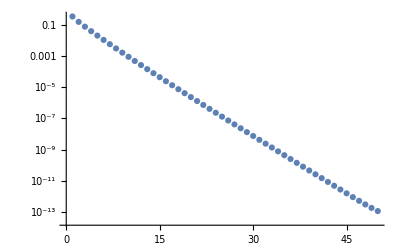

```mathematica
ListLogPlot[Table[Abs[j0sh[r,2.,1.,4.]-j0shList[r,2.,1.,4.,5]],{r,0.1,5,0.1}],PlotRange->All]
```

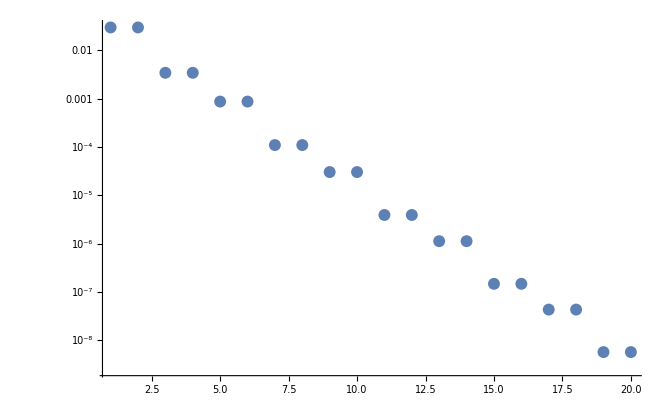

```mathematica
ListLogPlot[Table[Abs[j0sh[0.1,2.,1.,4.]-j0shList[1,2.,1.,4.,n]],{n,1,20}],PlotRange->All]
```

```mathematica
(* 检验 u33 的级数解. *)
zeroList = Table[FindRoot[Sinh[x]^2==x^2,{x,Log[2.m+1.]+Pi(m+0.5)ⅈ}],{m,1,100}];//AbsoluteTiming
zeroList[[1]]={x->2.2507286116018608+4.212392230490661 ⅈ};
z[m_?IntegerQ]:=x/.zeroList[[m]];
Export["Root_sinhx2_x2.dat",zeroList]
inverseOfz[m_?IntegerQ]:=1/(√(1+x^2)-1)/.zeroList[[m]];
time[eq_]:=Print[eq//AbsoluteTiming]
```

{0.0333006,Null}

Root_sinhx2_x2.dat

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Root_sinhx2_x2.dat"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Root_sinhx2_x2.dat"]]]
```

```mathematica
j0a2[r_,x3_,h_,H_]:=NIntegrate[BesselJ[0,r x]a2[x,h,H,x3],{x,0,Infinity},Method->"ExtrapolatingOscillatory"];
j0xdsh[r_,x3_,h_,H_]:=NIntegrate[BesselJ[0,r x]x raSinh2[x,h,H,x3],{x,0,Infinity},Method->"ExtrapolatingOscillatory"];
j1xsh[r_,x3_,h_,H_]:=NIntegrate[BesselJ[1,r x]x sh[x,h,H,x3],{x,0,Infinity},Method->"ExtrapolatingOscillatory"];

j0a2List[r_,x3_,h_,H_,nmax_]:=-Pi/H Sum[Im[(z[m]HankelH1[0,(r z[m])/H])/(√(1+z[m]^2)-1)
((√(1+z[m]^2)+1)(x3/H Sinh[(h z[m])/H]Cosh[(x3 z[m])/H]+h/H Sinh[(x3 z[m])/H]Cosh[(h z[m])/H]-1/z[m] Sinh[(x3 z[m])/H]Sinh[(h z[m])/H])
-(h x3)/H^2 z[m](√(1+z[m]^2)Cosh[((h+x3) z[m])/H]+Cosh[((x3-h) z[m])/H]-z[m]Sinh[((x3+h) z[m])/H])
-z[m](x3+h)/H Sinh[(h z[m])/H]Sinh[(x3 z[m])/H] )],{m,1,nmax}];
(* Subscript[u, αβ] = ∂/(∂Subscript[r, β])[Subscript[r, α]/ρ uab1(r,x3,h,H)]+∂/(∂Subscript[r, β])[2 Subscript[r, α]/ρ j1 1/x sh(r,x3,h,H)]+
		2 Subscript[δ, αβ]*j0sh(r,x3,h,H) - uab2(r,x3,h,H)∂/(∂Subscript[r, β])(Subscript[r, α]/ρ^2) *)
uab1[r_,x3_,h_,H_,nmax_]:=Pi/H Sum[Im[H HankelH1[1,(r z[m])/H](x3/H Sinh[(h z[m])/H]Cosh[(x3 z[m])/H]+h/H Sinh[(x3 z[m])/H]Cosh[(h z[m])/H]+1/z[m] Sinh[(x3 z[m])/H]Sinh[(h z[m])/H])
-1/(√(1+z[m]^2)-1)(z[m](x3+h)/H Sinh[(h z[m])/H]Sinh[(x3 z[m])/H] +
(h x3)/H^2 z[m](-√(1+z[m]^2)Cosh[((h+x3) z[m])/H]+Cosh[((x3-h) z[m])/H]+z[m]Sinh[((x3+h) z[m])/H]))
],{m,1,nmax}];
uab2[r_,x3_,h_,H_,nmax_]:=H(-6x3)/H*h/H(1-x3/H)(1-h/H);
```

```mathematica
Print[j0a2[1.,2.,1.,4.]//AbsoluteTiming]
```

{0.276067,-0.0948016}

```mathematica
Print[j0xdsh[1.,2.,1.,4.]//AbsoluteTiming]
```

{0.228078,-0.0159671}

```mathematica
Print[j0sh[1.,2.,1.,4.]//AbsoluteTiming]
Print[j0a2[##]+2j0sh[##]-1.j1xsh[##]&[1.,2.,1.,4.]//AbsoluteTiming]
```

{0.217947,0.174819}

{0.724871,0.0959846}

```mathematica
Print[u33[0,2.,2.,1.,4.]//AbsoluteTiming]
```

{3.015,-0.0254793}

```mathematica
Print[j0a2List[2.,2.,1.,4., 1]//AbsoluteTiming]
```

{0.000885767,-0.0304886}

```mathematica
$ExportFormats
```

{3DS,ACO,AIFF,AU,AVI,Base64,Binary,Bit,BMP,Byte,BYU,BZIP2,C,CDF,Character16,Character8,Complex128,Complex256,Complex64,CSV,CUR,DICOM,DIF,DIMACS,DOT,DXF,EMF,EPS,ExpressionML,FASTA,FASTQ,FCS,FITS,FLAC,FLV,GIF,Graph6,Graphlet,GraphML,GXL,GZIP,HarwellBoeing,HDF,HDF5,HTML,HTMLFragment,ICNS,ICO,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,JPEG,JPEG2000,JSON,JVX,KML,LEDA,List,LWO,MAT,MathML,Maya,MGF,MIDI,MOL,MOL2,MP3,MTX,MX,NASACDF,NB,NetCDF,NEXUS,NOFF,OBJ,OFF,OGG,Package,Pajek,PBM,PCX,PDB,PDF,PGM,PLY,PNG,PNM,POV,PPM,PXR,QuickTime,RawBitmap,RawJSON,Real128,Real32,Real64,RIB,RTF,SCT,SDF,SND,Sparse6,STL,String,SurferGrid,SVG,SWF,Table,TAR,TerminatedString,TeX,TeXFragment,Text,TGA,TGF,TIFF,TSV,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,UUE,VideoFrames,VRML,VTK,WAV,Wave64,WDX,WebP,WMF,X3D,XBM,XHTML,XHTMLMathML,XLS,XLSX,XML,XYZ,ZIP,ZPR}

```mathematica
EmbedCode[APIFunction[{"x"->"Integer"},#x^2&],"Python"]
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from Python:
Code
 | Copy to Clipboard
from urllib import urlencode
from urllib2 import urlopen

class WolframCloud:

    def wolfram_cloud_call(self, **args):
        arguments = dict([(key, arg) for key, arg in args.iteritems()])
        result = urlopen("http://www.wolframcloud.com/objects/b3588838-bc23-43ba-8f9e-39b29ef5c590", urlencode(arguments))
        return result.read()

    def call(self, x):
        textresult =  self.wolfram_cloud_call(x=x)
        return textresult

```mathematica
File
```

```mathematica
Directory[]
```

C:\Users\my\Documents

```mathematica
Module[{directory=SystemDialogInput["Directory"]},If[directory=!=$Canceled,SetDirectory[directory]]]
```

D:\Sync Work\Summer Internship

```mathematica
FileNames["*","D:\\Sync Work\\Summer Internship"]
```

{D:\Sync Work\Summer Internship\divU(8.3 night).png,D:\Sync Work\Summer Internship\ElectromagneticWavesFromALinearAntenna-author.nb,D:\Sync Work\Summer Internship\FlowAroundASphereAtFiniteReynoldsNumberByGalerkinMethod-author.nb,D:\Sync Work\Summer Internship\ganatos1980b.pdf,D:\Sync Work\Summer Internship\ganatos1980.pdf,D:\Sync Work\Summer Internship\Infinity sum.nb,D:\Sync Work\Summer Internship\Jeff Knupp-Writing Idiomatic Python 3-CreateSpace (2016).epub,D:\Sync Work\Summer Internship\Jeff_Knupp-Writing_Idiomatic_Python_3-CreateSpace_.pdf,D:\Sync Work\Summer Internship\Paul Wellin-Programming with Mathematica®_ An Introduction-Cambridge University Press (2013).pdf,D:\Sync Work\Summer Internship\点力场模拟.pptx,D:\Sync Work\Summer Internship\Progress, obstacle, future work.pptx,D:\Sync Work\Summer Internship\Project NoteBook.accdb,D:\Sync Work\Summer Internship\stokes Appendix.nb,D:\Sync Work\Summer Internship\Stokes Code.nb,D:\Sync Work\Summer Internship\stokes_derivative.nb,D:\Sync Work\Summer Internship\stokes_exp.nb,D:\Sync Work\Summer Internship\Stokes flow for a stokeslet between two parallel flat platesliron1976.pdf,D:\Sync Work\Summer Internship\Stokes_Infinity sum.nb,D:\Sync Work\Summer Internship\stokes.nb,D:\Sync Work\Summer Internship\stokes_series.nb,D:\Sync Work\Summer Internship\VectorFieldsByMyself.nb,D:\Sync Work\Summer Internship\VectorFieldsPlotExamples-author.nb,D:\Sync Work\Summer Internship\VectorFieldsStreamlineThroughAPoint-author.nb}

```mathematica
Directory[]
```

D:\Sync Work\Summer Internship

```mathematica
u33Nh[1.,0.,2.,1.,4.]
```

0.0959846